```mathematica
$Assumptions = q > 0 && q < 1&&v>0&&x>0&&y<0&&x>-y&&x<1
```

q>0&&q<1&&x>0&&y<0&&x>-y&&x<1

```mathematica
Subscript[I, 1]=∫_(-∞)^a -1/2(x/y-1)Exp[2s-s^2/(2v)]ⅆs
```

```mathematica
Subscript[I, 2]=1/(q y)∫_a^b (1/2-2 s/Log[(x+y)/(x-y)])Exp[-s^2/(2v)]ⅆs
```

```mathematica
Subscript[I, 3]=-1/(q(x^2+y^2))∫_b^∞ ((x^2-y^2)/(q(x^2+y^2))ⅇ^(-2s)+x)Exp[-s^2/(2v)]ⅆs
```

```mathematica
Subscript[I, tot]=1/(√(2π v))(Subscript[I, 1]+Subscript[I, 2]+Subscript[I, 3])
```

```mathematica
a=-1/2 Log[q(x-y)]
```

-1/2 Log[q (x-y)]

```mathematica
-1/2 Log[0.1(0.6)]
```

1.40671

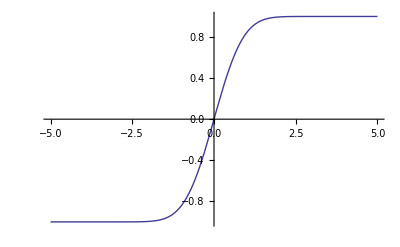

```mathematica
Plot[Erf[x],{x,-5,5}]
```

```mathematica
Series[Erf[ξ],{ξ,∞,1}]
```

1+ⅇ^(-ξ^2) (-1/(√π ξ)+O[1/ξ]^2)

```mathematica
Series[Erfc[ξ],{ξ,-∞,1}]
```

2+ⅇ^(-ξ^2) (1/(√π ξ)+O[1/ξ]^2)

```mathematica
Series[Erfc[ξ],{ξ,∞,1}]
```

ⅇ^(-ξ^2) (1/(√π ξ)+O[1/ξ]^2)

```mathematica
Series[ⅇ^(-ξ^2),{ξ,∞,1}]
```

ⅇ^(-ξ^2)

```mathematica
Series[1/(q^2 y^2/(ξ-q x)+(ξ-q x)),{ξ,∞,1}]
```

1/ξ+O[1/ξ]^2

```mathematica
∫_(-∞)^a Exp[2s-s^2/(2v)]/(√(2π v))ⅆs
```

1/2 ⅇ^(2 v) Erfc[(4 v+Log[q]+Log[x-y])/(2 √2 √v)]